## MICA: Measurement, Instrumentation, Control and Analysis

## Sigmoid Functions

#### Ian Hunter, MIT, 7 May 2026

```mathematica
Clear["Global`*"]
```

#### Objectives

The purpose of this MICA Module is to look at sigmoidal functions.

#### Note

You can progress through this Notebook by clicking on the   ■   at the start of each region of code.  This will execute  (evaluate) the region of code associated with   ■   and any results of the code execution will be generated and added to the Notebook. After inspecting the results and reading subsequent text you can use the mouse scroll wheel (if available) to scroll down to the next    ■     .

The whole Notebook can be executed by selecting Evaluation from the menu above and clicking on Evaluate Notebook. While it is OK to do this here, it can be potentially disastrous if this is done in MICA Notebooks containing code to run experiments.

#### Sigmoids

A sigmoidal function has an “S” shape as seen below. There are a wide variety of functions that can be considered to be sigmoids (see https://en.wikipedia.org/wiki/Sigmoid_function ). Sigmoidal functions are used in muscle physiology to describe the relationship between the calcium ion concentration around the molecules (e.g. actin, myosin, troponin, tropomyosin)  inside a muscle fiber and the force they produce. The Gaussian probability distribution function has a sigmoidal form. 
Here are a number of sigmoidal functions

#### Logistic function

The logistic function (see  https://en.wikipedia.org/wiki/Logistic_function ), σ(x)==1/(1+exp(-x)) is a solution to the differential equation y'==y (1-y).

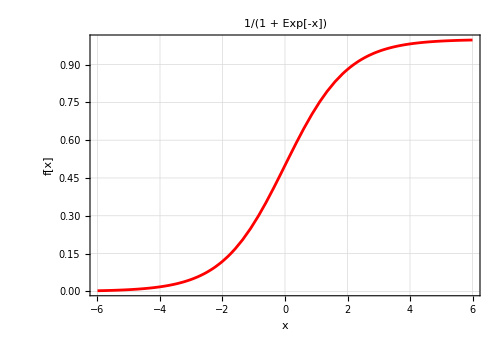

```mathematica
"■"; f1[x_]:=1/(1+Exp[-x]);
 Plot[f1[x],{x,-6,6},GridLines->Automatic,PlotStyle->Red,Frame->True,LabelStyle->{12,Black},AspectRatio->0.7,FrameLabel->{"x","f[x]"},PlotLabel->"1/(1 + Exp[-x])",PlotRange->All,ImageSize->500]
```

Note that in Mathematica this is the same as the LogisticSigmoid function:

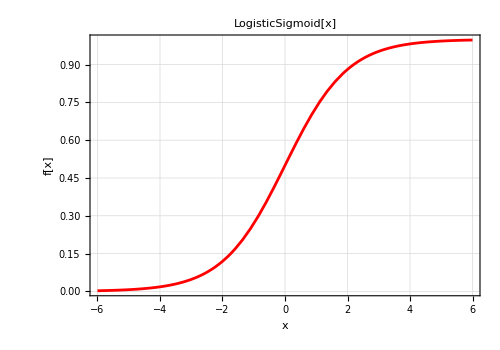

```mathematica
"■"; f1[x_]:=LogisticSigmoid[x];
 Plot[f1[x],{x,-6,6},GridLines->Automatic,PlotStyle->Red,Frame->True,LabelStyle->{12,Black},AspectRatio->0.7,FrameLabel->{"x","f[x]"},PlotLabel->"LogisticSigmoid[x]",PlotRange->All,ImageSize->500]
```

Often the Logistic function is modified such that it produces values that go from -1 to 1 :

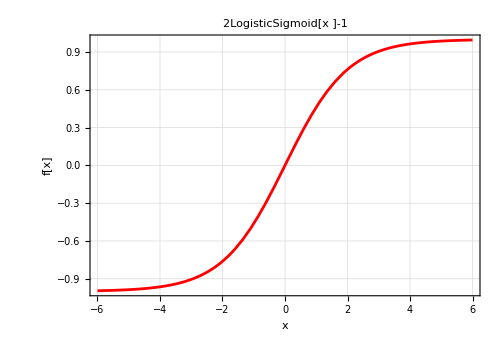

```mathematica
"■"; f1[x_]:=2LogisticSigmoid[x ]-1;Plot[f1[x],{x,-6,6},GridLines->Automatic,PlotStyle->Red,Frame->True,LabelStyle->{12,Black},AspectRatio->0.7,FrameLabel->{"x","f[x]"},PlotLabel->"2LogisticSigmoid[x ]-1",PlotRange->All,ImageSize->500]
```

And sometimes it is convenient to have it have a slope = 1 at 0 :

```mathematica
"■"; df[x_]:=f1'[x];
df[0]
```

1/2

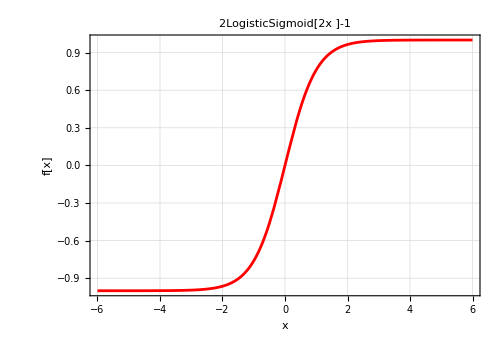

```mathematica
"■"; f1[x_]:=2LogisticSigmoid[2x ]-1;
Plot[f1[x],{x,-6,6},GridLines->Automatic,PlotStyle->Red,Frame->True,LabelStyle->{12,Black},AspectRatio->0.7,FrameLabel->{"x","f[x]"},PlotLabel->"2LogisticSigmoid[2x ]-1",PlotRange->All,ImageSize->500]
```

Check that the slope at 0 is 1 :

```mathematica
"■"; df[x_]:=f1'[x];
df[0]
```

1

#### Arctan function

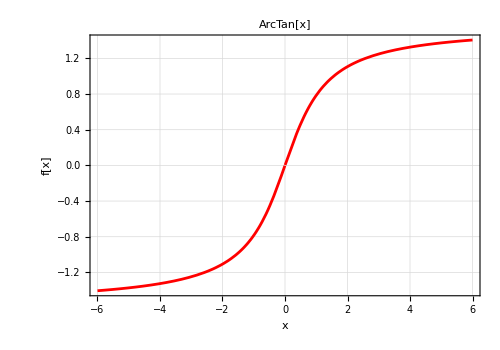

```mathematica
"■"; f2[x_]:=ArcTan[x];
Plot[f2[x],{x,-6,6},GridLines->Automatic,PlotStyle->Red,Frame->True,LabelStyle->{12,Black},AspectRatio->0.7,FrameLabel->{"x","f[x]"},PlotLabel->"ArcTan[x]",PlotRange->All,ImageSize->500]
```

The slope of this function at 0 is 1. But if we also want it to produce values which go from -1 to 1 then we modify it:

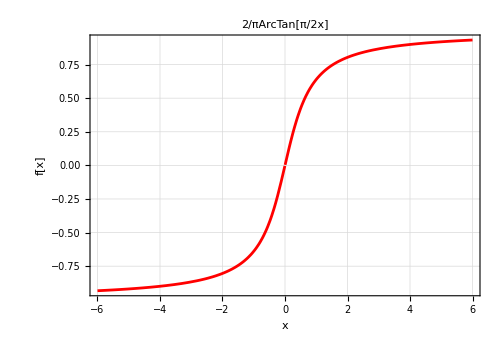

```mathematica
"■"; f2[x_]:=2/π ArcTan[π/2 x];
Plot[f2[x],{x,-6,6},GridLines->Automatic,PlotStyle->Red,Frame->True,LabelStyle->{12,Black},AspectRatio->0.7,FrameLabel->{"x","f[x]"},PlotLabel->"2/πArcTan[π/2x]",PlotRange->All,ImageSize->500]
```

Check that the slope at 0 is 1 :

```mathematica
"■"; df[x_]:=f2'[x];
df[0]
```

1

#### Tanh function

The tanh function is defined by  tanh(x)==(ⅇ^(2 x)-1)/(ⅇ^(2 x)+1)

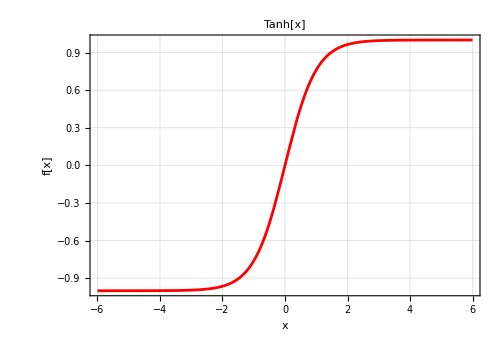

```mathematica
"■"; f3[x_]:=Tanh[x];
Plot[f3[x],{x,-6,6},GridLines->Automatic,PlotStyle->Red,Frame->True,LabelStyle->{12,Black},AspectRatio->0.7,FrameLabel->{"x","f[x]"},PlotLabel->"Tanh[x]",PlotRange->All,ImageSize->500]
```

Check that the slope at 0 is 1 :

```mathematica
"■"; df[x_]:=f3'[x];
df[0]
```

1

#### Error function

The error function (see https://en.wikipedia.org/wiki/Error_function  ), Erf[x], is the integral of the Gaussian density function, given by erf(x)=2/(√π)∫_0^x e^(-t^2)dt.

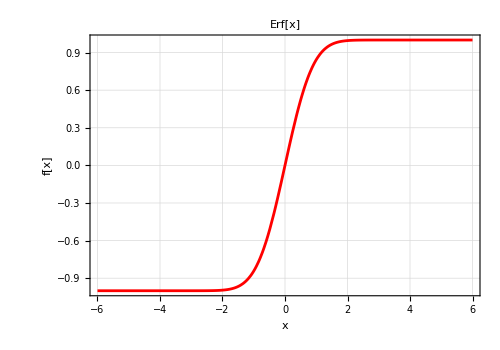

```mathematica
"■"; f4[x_]:=Erf[x];
Plot[f4[x],{x,-6,6},GridLines->Automatic,PlotStyle->Red,Frame->True,LabelStyle->{12,Black},AspectRatio->0.7,FrameLabel->{"x","f[x]"},PlotLabel->"Erf[x]",PlotRange->All,ImageSize->500]
```

If we want the slope at 0 to be 1 then we modify it to :

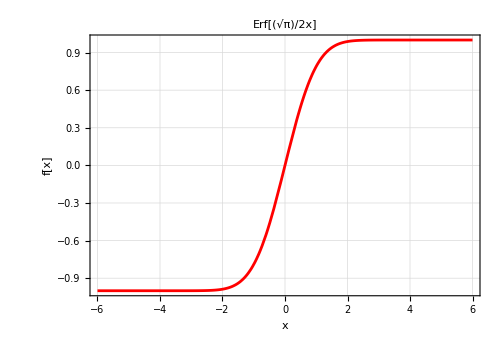

```mathematica
"■"; f4[x_]:=Erf[(√π)/2 x];
Plot[f4[x],{x,-6,6},GridLines->Automatic,PlotStyle->Red,Frame->True,LabelStyle->{12,Black},AspectRatio->0.7,FrameLabel->{"x","f[x]"},PlotLabel->"Erf[(√π)/2x]",PlotRange->All,ImageSize->500]
```

Check that the slope at 0 is 1 :

```mathematica
"■"; df[x_]:=f4'[x];
df[0]
```

1

#### Gudermannian function

The Gudermannian function (see https://en.wikipedia.org/wiki/Gudermannian_function ), Gudermannian[x] =  2 tan^-1(ⅇ^x)-π/2

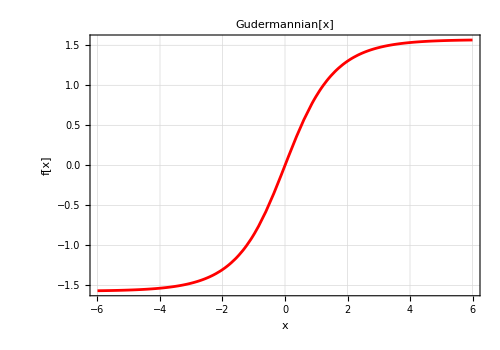

```mathematica
"■"; f5[x_]:=Gudermannian[x];
Plot[f5[x],{x,-6,6},GridLines->Automatic,PlotStyle->Red,Frame->True,LabelStyle->{12,Black},AspectRatio->0.7,FrameLabel->{"x","f[x]"},PlotLabel->"Gudermannian[x]",PlotRange->All,ImageSize->500]
```

If we want it to produce values that go from -1 to 1 and we want its slope at 0 to be 1 then we modify it to :

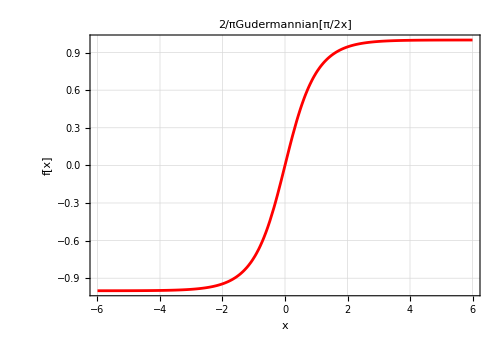

```mathematica
"■"; f5[x_]:=2/π Gudermannian[π/2 x];
Plot[f5[x],{x,-6,6},GridLines->Automatic,PlotStyle->Red,Frame->True,LabelStyle->{12,Black},AspectRatio->0.7,FrameLabel->{"x","f[x]"},PlotLabel->"2/πGudermannian[π/2x]",PlotRange->All,ImageSize->500]
```

Check that the slope at 0 is 1 :

```mathematica
"■"; df[x_]:=f5'[x];
df[0]
```

1

#### Another sigmoidal function

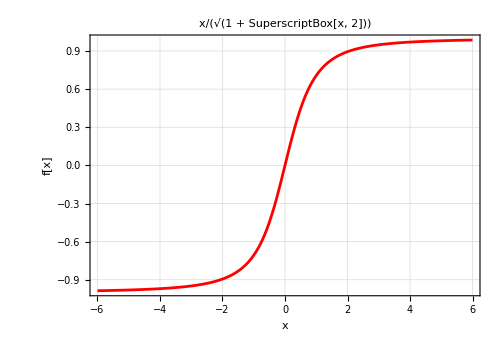

```mathematica
"■"; f6[x_]:=x/(√(1+x^2));
Plot[f6[x],{x,-6,6},GridLines->Automatic,PlotStyle->Red,Frame->True,LabelStyle->{12,Black},AspectRatio->0.7,FrameLabel->{"x","f[x]"},PlotLabel->"x/(√(1 + SuperscriptBox[x, 2]))",PlotRange->All,ImageSize->500]
```

Check that the slope at 0 is 1 :

```mathematica
"■"; df[x_]:=f6'[x];
df[0]
```

1

#### Yet another sigmoidal function

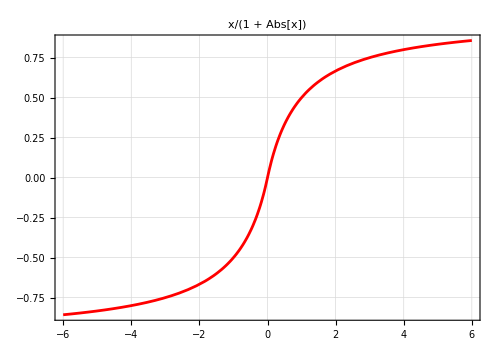

```mathematica
"■"; f7[x_]:=x/(1 + Abs[x]);
Plot[f7[x],{x,-6,6},GridLines->Automatic,PlotStyle->Red,Frame->True,LabelStyle->{12,Black},AspectRatio->0.7,PlotLabel->"x/(1  +  Abs[x])",PlotRange->All,ImageSize->500]
```

Check that the slope at 0 is 1 :

```mathematica
"■"; df[x_]:=f7'[x];
df[0]
```

1

#### Sigmoidal function comparison

Lets plot together all the sigmoidal functions shown above (in the form with a slope at 0 of 1 (shown as a dashed red line)):

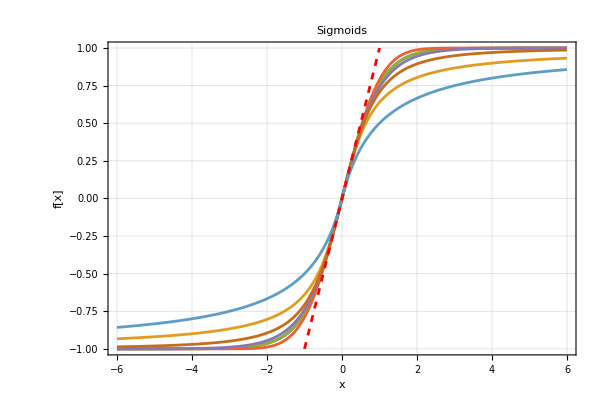

```mathematica
"■"; Show[
Plot[{f1[x],f2[x],f3[x],f4[x],f5[x],f6[x],f7[x]},{x,-6,6},GridLines->Automatic,Frame->True,LabelStyle->{12,Black},AspectRatio->0.7,FrameLabel->{"x","f[x]"},PlotLabel->"Sigmoids",PlotRange->All,ImageSize->600],
Plot[x,{x,-1,1},PlotStyle->{Red, Dashed}]]
```